# ArgMax

sei a>0 c <= q <= d dann ist ArgMax(a q^2+b q) gleich A

```mathematica
A[a_,b_,c_,d_]:=Piecewise[{{c,Abs[c+b/2/a]>Abs[d+b/2/a]}},d]
```

1

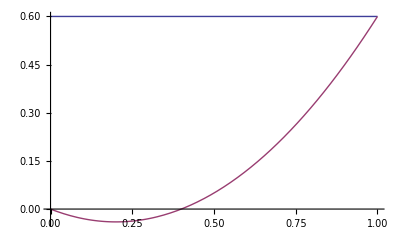

```mathematica
c=0;d=1;a=1;b=-0.4;A[a,b,c,d]
Plot[{a A[a,b,c,d]^2+b A[a,b,c,d],a q^2+b q},{q,c,d}]
```